```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### cluster data, vary E20

```mathematica
thisData=Import["data_mechanism2//mechanism2_stabilityDiagram_varyGamma_beta1_1.mx"];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
thisParamSet=Import["data_mechanism2//mechanism2_stabilityDiagram_varyGamma_params.mx"];
```

```mathematica
varyGamma=True;
```

```mathematica
ss1={};
ss3={};
```

```mathematica
For[i=1,i<=Length[thisData],i++,

For[j=1,j<=Length[thisData[[i]]],j++,

(*if gamma is the control variable, then we plot in 1/gamma*)
If[varyGamma,thisCoord={thisData[[i,j,1]],1/thisData[[i,j,2]]};,thisCoord={thisData[[i,j,1]],thisData[[i,j,2]]}];
(*check that there's an actual solution*)
If[Length[thisData[i,j,3,1]]>1,
If[Length[thisData[[i,j,3]]]==1,AppendTo[ss1,thisCoord],AppendTo[ss3,thisCoord]];
];
]
]
```

```mathematica
(*Export["stabilityPhaseDiagram_mechanism1_varyE20.png",%,ImageResolution->200]*)
```

```mathematica
ss1Height=Table[{ss1[[i,1]],ss1[[i,2]],-1},{i,Length[ss1]}];
```

```mathematica
ss3Height=Table[{ss3[[i,1]],ss3[[i,2]],1},{i,Length[ss3]}];
```

```mathematica
allPoints=Join[ss1Height,ss3Height];
```

```mathematica
(*convert allPoints to matrix format*)
```

```mathematica
xList=DeleteDuplicates[allPoints[[;;,1]]];
yList=DeleteDuplicates[allPoints[[;;,2]]]//Reverse;
```

```mathematica
plottingMatrix=ConstantArray[0,{Length[yList],Length[xList]}];
```

```mathematica
For[i=1,i<=Length[allPoints],i++,

thisPoint=allPoints[[i]];

rowIndex=Position[yList,thisPoint[[2]]][[1,1]];
colIndex=Position[xList,thisPoint[[1]]][[1,1]];

plottingMatrix[[rowIndex,colIndex]]=thisPoint[[3]];
]
```

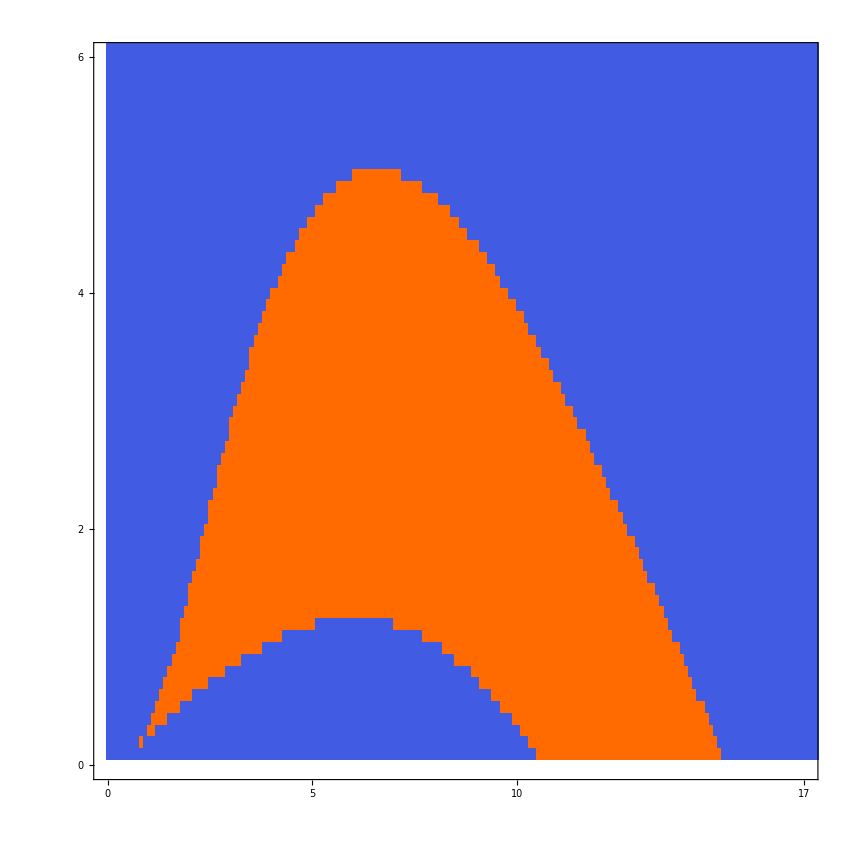

```mathematica
MatrixPlot[plottingMatrix,AspectRatio->1,Frame->{True,True,False,False},(*FrameLabel->{"Effector interaction strength 1/γ_1","Effector load E_1"},*)LabelStyle->Directive[Black,30],DataRange->{{xList[[1]],xList[[-1]]},{yList[[-1]],yList[[1]]}},PlotRange->{{0,17},{0,6}}]
```

```mathematica
(*Export["interference_mechanism2_varyGamma_phaseDiagram.png",%,ImageResolution->200]*)
```

interference_mechanism2_varyGamma_phaseDiagram.png